{0.0005,0.001,0.002,0.003,0.005,0.01}

{164.771,161.281,156.025,155.64,153.951,151.474}

{0.714331,0.566965,0.45,0.393111,0.331563,0.263162}

{117.701,91.4405,70.2112,61.1838,51.0445,39.8622}

{1.,1.,1.,1.,1.,1.}

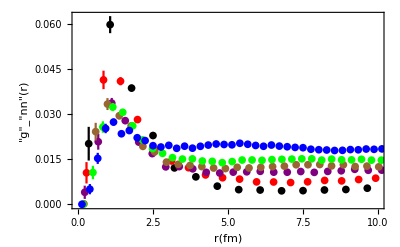

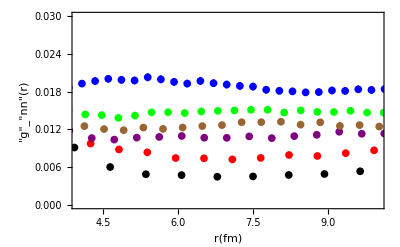

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
Needs["PlotLegends`"]

n=8; (*Which distribution to plot, np0=2, np1=4, pp=6, nn=8*)
joined=False;
corrtype=2;
norm1=True;
errorbars=True;

If[n==2,sys="np0"];
If[n==4,sys="np1"];
If[n==6,sys="pp"];
If[n==8,sys="nn"];

If[corrtype==1,
density={"0.0005","0.002","0.003","0.005","0.01"};
colors={Black,Purple,Brown,Green,Blue};
corr="lin",
density={"0.0005","0.001","0.002","0.003","0.005","0.01"};
colors={Black,Red,Purple,Brown,Green,Blue};
corr="ip"];
len=Length[density];

p=Range[len]*0;
intbefore=Range[len]*0;
testsum=Range[len]*0;
testdiff=Range[len]*0;
intafter=Range[len]*0;
For[i=1,i≤len,i++,
data=Import[StringJoin["gofrnp_",density[[i]],"_",corr,".dmc"],"Table"];
xmax=Length[data]-2;
data=Transpose[data[[4;;xmax]]];
intbefore[[i]]=Total[data[[n]]]*(data[[1,2]]-data[[1,1]]);
testsum[[i]]=Total[data[[n]]];
testdiff[[i]]=(data[[1,2]]-data[[1,1]]);
If[norm1,norm=(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
If[norm1,data[[n]]=data[[n]]/norm];
If[norm1,data[[n+1]]=data[[n+1]]/norm];
If[errorbars,p[[i]]=ErrorListPlot[Transpose[{data[[1]],data[[n]],data[[n+1]]}],PlotStyle->colors[[i]],Joined->joined,PlotRange->All],p[[i]]=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->colors[[i]],Joined->joined]];
intafter[[i]]=Total[data[[n]]]*(data[[1,2]]-data[[1,1]]);
]
density
testsum
testdiff
intbefore
intafter
Show[p,PlotRange->{{0,10},All},Frame->{{True,False},{True,False}},AxesOrigin->{0,0},FrameLabel->{"r(fm)",StringJoin[ToString[Subscript["g", sys],StandardForm],"(r)"]},FrameStyle->Directive[Black,12],PlotRangePadding->0]
Show[p,PlotRange->{{4,10},{0,0.03}},Frame->{{True,False},{True,False}},AxesOrigin->{0,0},FrameLabel->{"r(fm)",StringJoin[ToString[Subscript["g", sys],StandardForm],"(r)"]},FrameStyle->Directive[Black,12],PlotRangePadding->0]
```

# Old stuff

#### Plot g(r) data for various channels normalized so that they integrate to 1

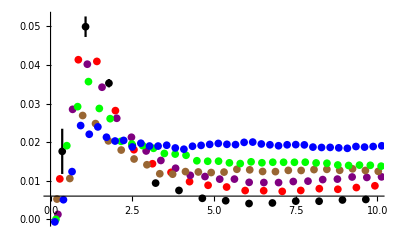

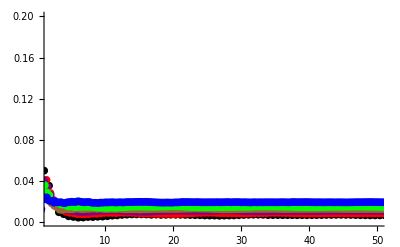

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]

joined=False;
n=8; (*Which distribution to plot, np0=2, np1=4, pp=6, nn=8*)
corr="lin";(*Which correlation to plot "lin" or "ip"*)
norm1=True;
errorbars=True;

data=Import[StringJoin["gofrnp_0.0005_",corr,".dmc"],"Table"];
xmax=Length[data]-2;
data=Transpose[data[[4;;xmax]]];
If[norm1,norm=(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
If[norm1,data[[n]]=data[[n]]/norm];
If[norm1,data[[n+1]]=data[[n+1]]/norm];
If[errorbars,p1=ErrorListPlot[Transpose[{data[[1]],data[[n]],data[[n+1]]}],PlotStyle->Black,Joined->joined],p1=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->Black,Joined->joined]];

data=Import[StringJoin["gofrnp_0.001_ip.dmc"],"Table"];
xmax=Length[data]-2;
data=Transpose[data[[4;;xmax]]];
If[norm1,norm=(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
If[norm1,data[[n]]=data[[n]]/norm];
If[norm1,data[[n+1]]=data[[n+1]]/norm];
p2=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->Red,Joined->joined];

data=Import[StringJoin["gofrnp_0.002_",corr,".dmc"],"Table"];
xmax=Length[data]-2;
data=Transpose[data[[4;;xmax]]];
If[norm1,norm=(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
If[norm1,data[[n]]=data[[n]]/norm];
If[norm1,data[[n+1]]=data[[n+1]]/norm];
p3=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->Purple,Joined->joined];

data=Import[StringJoin["gofrnp_0.003_",corr,".dmc"],"Table"];
xmax=Length[data]-2;
data=Transpose[data[[4;;xmax]]];
If[norm1,norm=(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
If[norm1,data[[n]]=data[[n]]/norm];
If[norm1,data[[n+1]]=data[[n+1]]/norm];
p4=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->Brown,Joined->joined];

data=Import[StringJoin["gofrnp_0.005_",corr,".dmc"],"Table"];
xmax=Length[data]-2;
data=Transpose[data[[4;;xmax]]];
If[norm1,norm=(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
If[norm1,data[[n]]=data[[n]]/norm];
If[norm1,data[[n+1]]=data[[n+1]]/norm];
p5=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->Green,Joined->joined];

data=Import[StringJoin["gofrnp_0.01_",corr,".dmc"],"Table"];
xmax=Length[data]-2;
data=Transpose[data[[4;;xmax]]];
If[norm1,norm=(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
If[norm1,data[[n]]=data[[n]]/norm];
If[norm1,data[[n+1]]=data[[n+1]]/norm];
p6=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->Blue,Joined->joined];

Show[p1,p2,p3,p4,p5,p6,PlotRange->{{0,10},All}]
Show[p1,p2,p3,p4,p5,p6,PlotRange->{{2,50},{0,0.2}},PlotRange->All]
```

Make sure it integrates to 1

```mathematica
n=8;
data=Import[StringJoin["gofrnp_0.0005_",corr,".dmc"],"Table"];
data=Transpose[data[[4;;Length[data]-2]]];
If[True,data[[n]]=data[[n]]/(Total[data[[n]]]*(data[[1,2]]-data[[1,1]]))];
p1=ListPlot[Transpose[{data[[1]],data[[n]]}],PlotStyle->Black,Joined->joined];
Total[data[[n]]]*(data[[1,2]]-data[[1,1]])
```

1.

Make sure the interpolated integration is similar to the integration used for normalization

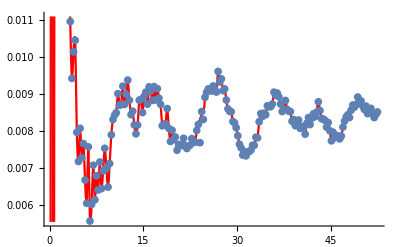

0.486225

0.48586

```mathematica
n=6;
data=Import[StringJoin["gofrnp_0.01_",corr,".dmc"],"Table"];
data=Transpose[data[[4;;Length[data]-2]]];
mydata=Transpose[{data[[1]],data[[n]]}];
xmin=mydata[[1,1]];
xmax=Max[data[[1]]];
myint=Interpolation[mydata,InterpolationOrder->3];
p1=Plot[myint[x],{x,xmin,xmax},PlotStyle->Red];
p2=ListPlot[mydata];
Show[p1,p2]
Integrate[myint[x],{x,xmin,xmax}]
Total[data[[n]]]*(data[[1,2]]-data[[1,1]])
```